# Задача 1

# Метод на разполовяването

```mathematica
f[x_]:=  (-360Cos[x] + x^3  + 23)/(9 - x^2)
```

```mathematica
f[x]
```

(23+x^3-360 Cos[x])/(9-x^2)

## 1. Визуализация на функцията

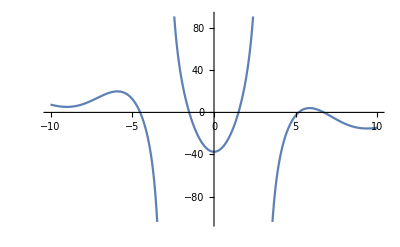

```mathematica
Plot[f[x],{x,-10,10}]
```

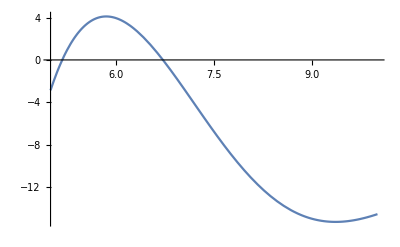

```mathematica
Plot[f[x],{x,5,10}]
```

Общ брой корени - 5

## 2. Да се локализира един от корените.

Локализираме най-малкия корен

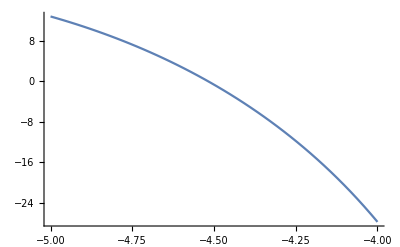

```mathematica
Plot[f[x],{x,-5,-4}]
```

```mathematica
f[-5.]
```

12.7574

```mathematica
f[-4.]
```

-27.7588

Извод:
(1) Функцията е непрекъсната, защото е сума от непрекъснати функции (полином и синус)
(2) f(-5) = 12.7574... > 0
       f(-4) = -27.7588... < 0
       => Функцията има различни знаци в двата края на разглеждания интервал [-5; -4].
       От (1) и (2) следва, че функцията има поне един корен в разглеждания интервал [-5; -4].

## 3. Уточнете локализирания корен по метода на разполовяването.

```mathematica
f[x_]:=  (-360Cos[x] + x^3  + 23)/(9 - x^2)
a =  -5.;b = -4.;
For[n = 0, n <4 , n++, 
Print["n = ",n, " a_n = ",a, " b_n = ",b, " m_n = ",m =  (a + b)/2  ,  " f(m_n) = ",f[m], " ε_n = ", (b - a)/2];
If[f[m] > 0, b = m, a = m]
]
```

n = 0 a_n = -5. b_n = -4. m_n = -4.5 f(m_n) = -0.68991 ε_n = 0.5

n = 1 a_n = -4.5 b_n = -4. m_n = -4.25 f(m_n) = -11.7877 ε_n = 0.25

n = 2 a_n = -4.25 b_n = -4. m_n = -4.125 f(m_n) = -19.0027 ε_n = 0.125

n = 3 a_n = -4.125 b_n = -4. m_n = -4.0625 f(m_n) = -23.1597 ε_n = 0.0625

## 4. Оценка на грешката.

Цикъл при достигане на определена предварително зададена точност (със стоп-критерий):

```mathematica
f[x_]:=  (-360Cos[x] + x^3  + 23)/(9 - x^2)
a =  -5.;b = -4.;
epszad = 0.000001;
eps =  Infinity;
For[n = 0, eps > epszad , n++, 
Print["n = ",n, " a_n = ",a, " b_n = ",b, " m_n = ",m =  (a + b)/2  ,  " f(m_n) = ",f[m], " ε_n = ", eps = (b - a)/2];
If[f[m] > 0, b = m, a = m]
]
```

n = 0 a_n = -5. b_n = -4. m_n = -4.5 f(m_n) = -0.68991 ε_n = 0.5

n = 1 a_n = -4.5 b_n = -4. m_n = -4.25 f(m_n) = -11.7877 ε_n = 0.25

n = 2 a_n = -4.25 b_n = -4. m_n = -4.125 f(m_n) = -19.0027 ε_n = 0.125

n = 3 a_n = -4.125 b_n = -4. m_n = -4.0625 f(m_n) = -23.1597 ε_n = 0.0625

n = 4 a_n = -4.0625 b_n = -4. m_n = -4.03125 f(m_n) = -25.3997 ε_n = 0.03125

n = 5 a_n = -4.03125 b_n = -4. m_n = -4.01563 f(m_n) = -26.5638 ε_n = 0.015625

n = 6 a_n = -4.01563 b_n = -4. m_n = -4.00781 f(m_n) = -27.1573 ε_n = 0.0078125

n = 7 a_n = -4.00781 b_n = -4. m_n = -4.00391 f(m_n) = -27.4571 ε_n = 0.00390625

n = 8 a_n = -4.00391 b_n = -4. m_n = -4.00195 f(m_n) = -27.6077 ε_n = 0.00195313

n = 9 a_n = -4.00195 b_n = -4. m_n = -4.00098 f(m_n) = -27.6832 ε_n = 0.000976563

n = 10 a_n = -4.00098 b_n = -4. m_n = -4.00049 f(m_n) = -27.721 ε_n = 0.000488281

n = 11 a_n = -4.00049 b_n = -4. m_n = -4.00024 f(m_n) = -27.7399 ε_n = 0.000244141

n = 12 a_n = -4.00024 b_n = -4. m_n = -4.00012 f(m_n) = -27.7494 ε_n = 0.00012207

n = 13 a_n = -4.00012 b_n = -4. m_n = -4.00006 f(m_n) = -27.7541 ε_n = 0.0000610352

n = 14 a_n = -4.00006 b_n = -4. m_n = -4.00003 f(m_n) = -27.7564 ε_n = 0.0000305176

n = 15 a_n = -4.00003 b_n = -4. m_n = -4.00002 f(m_n) = -27.7576 ε_n = 0.0000152588

n = 16 a_n = -4.00002 b_n = -4. m_n = -4.00001 f(m_n) = -27.7582 ε_n = 7.62939×10^-6

n = 17 a_n = -4.00001 b_n = -4. m_n = -4. f(m_n) = -27.7585 ε_n = 3.8147×10^-6

n = 18 a_n = -4. b_n = -4. m_n = -4. f(m_n) = -27.7587 ε_n = 1.90735×10^-6

n = 19 a_n = -4. b_n = -4. m_n = -4. f(m_n) = -27.7587 ε_n = 9.53674×10^-7

За достигане на точност 10^-6 са ни необходими 19 итерации.